```mathematica
2-2
```

0

# Perfectly Alternating Graphs

Nicholas Wheeler
1 October 2011

### Introduction

I construct here a few examples of graphs that acquire interest from this fact: random walkers on such graphs always know—from the color of the node on which they stand—whether they have executed an even or odd number of steps in arriving at that node. The generative transition matrices always have spectra of the form

{-1, +1, other eigenvalues with absolute value < 1}

and therefore lead asymptotically to states that "blink."

```mathematica
p1={1,1};
p2={1, -1};
p3={-1,-1};
p4={-1,1};
```

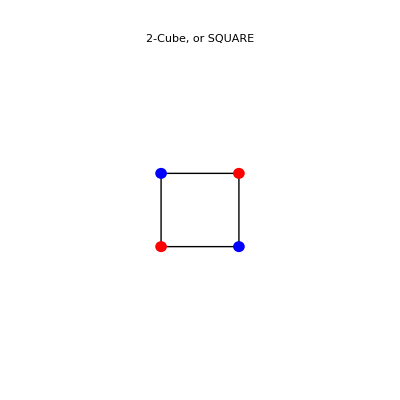

```mathematica
Cube2=Graphics[{
Line[{p1,p2}],
Line[{p2,p3}],
Line[{p3,p4}],
Line[{p4,p1}],
{Red, Disk[p1,.15]},
{Blue, Disk[p2,.15]},
{Red, Disk[p3,.15]},
{Blue, Disk[p4,.15]},
{White,Line[{4.2p1,4.2p2}]},
{White,Line[{4.2p2,4.2p3}]},
{White,Line[{4.2p3,4.2p4}]},
{White,Line[{4.2p4,4.2p1}]}},
PlotLabel->"2-Cube, or SQUARE"]
```

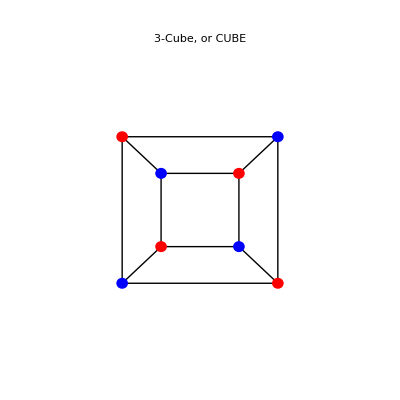

```mathematica
Cube3=Graphics[{
Line[{p1,p2}],
Line[{p2,p3}],
Line[{p3,p4}],
Line[{p4,p1}],
Line[{2p1,2p2}],
Line[{2p2,2p3}],
Line[{2p3,2p4}],
Line[{2p4,2p1}],
Line[{p1,2p1}],
Line[{p2,2p2}],
Line[{p3,2p3}],
Line[{p4,2p4}],
{Red, Disk[p1,.15]},
{Blue, Disk[p2,.15]},
{Red, Disk[p3,.15]},
{Blue, Disk[p4,.15]},
{Blue, Disk[2p1,.15]},
{Red, Disk[2p2,.15]},
{Blue, Disk[2p3,.15]},
{Red, Disk[2p4,.15]},
{White,Line[{4.2p1,4.2p2}]},
{White,Line[{4.2p2,4.2p3}]},
{White,Line[{4.2p3,4.2p4}]},
{White,Line[{4.2p4,4.2p1}]}},
PlotLabel->"3-Cube, or CUBE"]
```

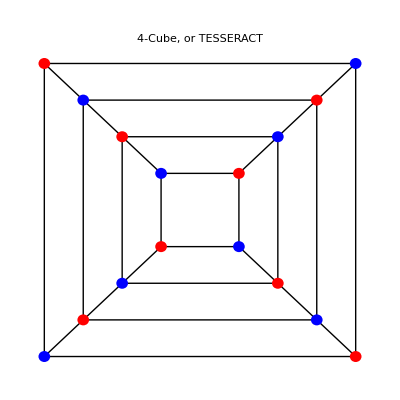

```mathematica
Cube4=Graphics[{
Line[{p1,p2}],
Line[{p2,p3}],
Line[{p3,p4}],
Line[{p4,p1}],
Line[{2p1,2p2}],
Line[{2p2,2p3}],
Line[{2p3,2p4}],
Line[{2p4,2p1}],
Line[{3p1,3p2}],
Line[{3p2,3p3}],
Line[{3p3,3p4}],
Line[{3p4,3p1}],
Line[{4p1,4p2}],
Line[{4p2,4p3}],
Line[{4p3,4p4}],
Line[{4p4,4p1}],
Line[{p1,4p1}],
Line[{p2,4p2}],
Line[{p3,4p3}],
Line[{p4,4p4}],
{Red, Disk[p1,.15]},
{Blue, Disk[p2,.15]},
{Red, Disk[p3,.15]},
{Blue, Disk[p4,.15]},
{Blue, Disk[2p1,.15]},
{Red, Disk[2p2,.15]},
{Blue, Disk[2p3,.15]},
{Red, Disk[2p4,.15]},
{Red, Disk[3p1,.15]},
{Blue, Disk[3p2,.15]},
{Red, Disk[3p3,.15]},
{Blue, Disk[3p4,.15]},
{Blue, Disk[4p1,.15]},
{Red, Disk[4p2,.15]},
{Blue, Disk[4p3,.15]},
{Red, Disk[4p4,.15]},
{White,Line[{4.2p1,4.2p2}]},
{White,Line[{4.2p2,4.2p3}]},
{White,Line[{4.2p3,4.2p4}]},
{White,Line[{4.2p4,4.2p1}]}},
PlotLabel->"4-Cube, or TESSERACT"]
```

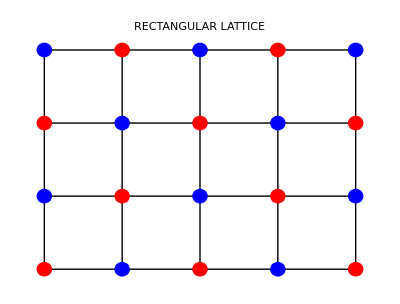

```mathematica
RectangularLattice=Graphics[{
Line[{{1,1},{1,4}}],
Line[{{2,1},{2,4}}],
Line[{{3,1},{3,4}}],
Line[{{4,1},{4,4}}],
Line[{{5,1},{5,4}}],
Line[{{1,1},{5,1}}],
Line[{{1,2},{5,2}}],
Line[{{1,3},{5,3}}],
Line[{{1,4},{5,4}}],
{Red,Disk[{1,1},0.1]},
{Blue,Disk[{2,1},0.1]},
{Red,Disk[{3,1},0.1]},
{Blue,Disk[{4,1},0.1]},
{Red,Disk[{5,1},0.1]},
{Red,Disk[{1,3},0.1]},
{Blue,Disk[{2,3},0.1]},
{Red,Disk[{3,3},0.1]},
{Blue,Disk[{4,3},0.1]},
{Red,Disk[{5,3},0.1]},
{Blue,Disk[{1,2},0.1]},
{Red,Disk[{2,2},0.1]},
{Blue,Disk[{3,2},0.1]},
{Red,Disk[{4,2},0.1]},
{Blue,Disk[{5,2},0.1]},
{Blue,Disk[{1,4},0.1]},
{Red,Disk[{2,4},0.1]},
{Blue,Disk[{3,4},0.1]},
{Red,Disk[{4,4},0.1]},
{Blue,Disk[{5,4},0.1]}
},PlotLabel->"RECTANGULAR LATTICE"]
```

```mathematica
q0={0,0};
q1={Cos[π/2],Sin[π/2]};
q2={Cos[π/2-(2π)/3],Sin[π/2-(2π)/3]};
q3={Cos[π/2-2(2π)/3],Sin[π/2-2(2π)/3]};
```

```mathematica
h=2Cos[π/6];
```

```mathematica
Q0[n_]:={n h,0};
Q1[n_]:={Cos[π/2]+n h,Sin[π/2]};
Q2[n_]:={Cos[π/2-(2π)/3]+n h,Sin[π/2-(2π)/3]};
Q3[n_]:={Cos[π/2-2(2π)/3]+n h,Sin[π/2-2(2π)/3]};
```

```mathematica
t={Cos[π/6],1+Sin[π/6]};
```

```mathematica
u={0,2+2Sin[π/6]};
```

```mathematica
v=t+u;
```

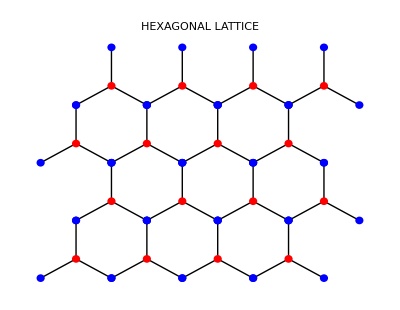

```mathematica
HexagonalLattice=Graphics[{
Line[{q0,q1}],
Line[{q0,q2}],
Line[{q0,q3}],
{Red,Disk[q0,0.1]},
{Blue,Disk[q1,0.1]},
{Blue,Disk[q2,0.1]},
{Blue,Disk[q3,0.1]},
Line[{Q0[1],Q1[1]}],
Line[{Q0[1],Q2[1]}],
Line[{Q0[1],Q3[1]}],
{Red,Disk[Q0[1],0.1]},
{Blue,Disk[Q1[1],0.1]},
{Blue,Disk[Q2[1],0.1]},
{Blue,Disk[Q3[1],0.1]},
Line[{Q0[2],Q1[2]}],
Line[{Q0[2],Q2[2]}],
Line[{Q0[2],Q3[2]}],
{Red,Disk[Q0[2],0.1]},
{Blue,Disk[Q1[2],0.1]},
{Blue,Disk[Q2[2],0.1]},
{Blue,Disk[Q3[2],0.1]},
Line[{Q0[3],Q1[3]}],
Line[{Q0[3],Q2[3]}],
Line[{Q0[3],Q3[3]}],
{Red,Disk[Q0[3],0.1]},
{Blue,Disk[Q1[3],0.1]},
{Blue,Disk[Q2[3],0.1]},
{Blue,Disk[Q3[3],0.1]},
Line[{q0+t,q1+t}],
Line[{q0+t,q2+t}],
Line[{q0+t,q3+t}],
{Red,Disk[q0+t,0.1]},
{Blue,Disk[q1+t,0.1]},
{Blue,Disk[q2+t,0.1]},
{Blue,Disk[q3+t,0.1]},
Line[{Q0[1]+t,Q1[1]+t}],
Line[{Q0[1]+t,Q2[1]+t}],
Line[{Q0[1]+t,Q3[1]+t}],
{Red,Disk[Q0[1]+t,0.1]},
{Blue,Disk[Q1[1]+t,0.1]},
{Blue,Disk[Q2[1]+t,0.1]},
{Blue,Disk[Q3[1]+t,0.1]},
Line[{Q0[2]+t,Q1[2]+t}],
Line[{Q0[2]+t,Q2[2]+t}],
Line[{Q0[2]+t,Q3[2]+t}],
{Red,Disk[Q0[2]+t,0.1]},
{Blue,Disk[Q1[2]+t,0.1]},
{Blue,Disk[Q2[2]+t,0.1]},
{Blue,Disk[Q3[2]+t,0.1]},
Line[{Q0[3]+t,Q1[3]+t}],
Line[{Q0[3]+t,Q2[3]+t}],
Line[{Q0[3]+t,Q3[3]+t}],
{Red,Disk[Q0[3]+t,0.1]},
{Blue,Disk[Q1[3]+t,0.1]},
{Blue,Disk[Q2[3]+t,0.1]},
{Blue,Disk[Q3[3]+t,0.1]},
Line[{q0+u,q1+u}],
Line[{q0+u,q2+u}],
Line[{q0+u,q3+u}],
{Red,Disk[q0+u,0.1]},
{Blue,Disk[q1+u,0.1]},
{Blue,Disk[q2+u,0.1]},
{Blue,Disk[q3+u,0.1]},
Line[{Q0[1]+u,Q1[1]+u}],
Line[{Q0[1]+u,Q2[1]+u}],
Line[{Q0[1]+u,Q3[1]+u}],
{Red,Disk[Q0[1]+u,0.1]},
{Blue,Disk[Q1[1]+u,0.1]},
{Blue,Disk[Q2[1]+u,0.1]},
{Blue,Disk[Q3[1]+u,0.1]},
Line[{Q0[2]+u,Q1[2]+u}],
Line[{Q0[2]+u,Q2[2]+u}],
Line[{Q0[2]+u,Q3[2]+u}],
{Red,Disk[Q0[2]+u,0.1]},
{Blue,Disk[Q1[2]+u,0.1]},
{Blue,Disk[Q2[2]+u,0.1]},
{Blue,Disk[Q3[2]+u,0.1]},
Line[{Q0[3]+u,Q1[3]+u}],
Line[{Q0[3]+u,Q2[3]+u}],
Line[{Q0[3]+u,Q3[3]+u}],
{Red,Disk[Q0[3]+u,0.1]},
{Blue,Disk[Q1[3]+u,0.1]},
{Blue,Disk[Q2[3]+u,0.1]},
{Blue,Disk[Q3[3]+u,0.1]},
Line[{q0+v,q1+v}],
Line[{q0+v,q2+v}],
Line[{q0+v,q3+v}],
{Red,Disk[q0+v,0.1]},
{Blue,Disk[q1+v,0.1]},
{Blue,Disk[q2+v,0.1]},
{Blue,Disk[q3+v,0.1]},
Line[{Q0[1]+v,Q1[1]+v}],
Line[{Q0[1]+v,Q2[1]+v}],
Line[{Q0[1]+v,Q3[1]+v}],
{Red,Disk[Q0[1]+v,0.1]},
{Blue,Disk[Q1[1]+v,0.1]},
{Blue,Disk[Q2[1]+v,0.1]},
{Blue,Disk[Q3[1]+v,0.1]},
Line[{Q0[2]+v,Q1[2]+v}],
Line[{Q0[2]+v,Q2[2]+v}],
Line[{Q0[2]+v,Q3[2]+v}],
{Red,Disk[Q0[2]+v,0.1]},
{Blue,Disk[Q1[2]+v,0.1]},
{Blue,Disk[Q2[2]+v,0.1]},
{Blue,Disk[Q3[2]+v,0.1]},
Line[{Q0[3]+v,Q1[3]+v}],
Line[{Q0[3]+v,Q2[3]+v}],
Line[{Q0[3]+v,Q3[3]+v}],
{Red,Disk[Q0[3]+v,0.1]},
{Blue,Disk[Q1[3]+v,0.1]},
{Blue,Disk[Q2[3]+v,0.1]},
{Blue,Disk[Q3[3]+v,0.1]}},PlotLabel->"HEXAGONAL LATTICE"]
```

```mathematica
a={0,0};
b1={1,k 2};
b2={1,-2k};
c1={2,3k};
c2={2,1k};
c3={2,-1k};
c4={2,-3k};
d1={3,2k};
d2={3,-2k};
e={4,0};
f1={0,-5k};
f2={2,-5k};
f3={4,-5k};
```

```mathematica
k=.3;
```

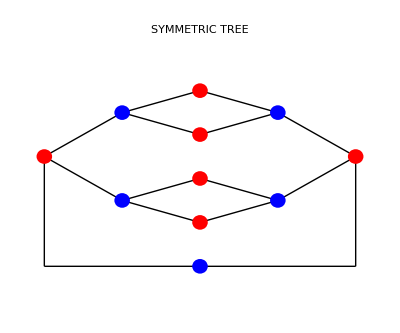

```mathematica
SymmetricTree=Graphics[{
Line[{a,b1}],
Line[{a,b2}],
Line[{b1,c1}],
Line[{b1,c2}],
Line[{b2,c3}],
Line[{b2,c4}],
Line[{c1,d1}],
Line[{c2,d1}],
Line[{c3,d2}],
Line[{c4,d2}],
Line[{d1,e}],
Line[{d2,e}],
Line[{e,f3}],
Line[{f3,f2}],
Line[{f2,f1}],
Line[{f1,a}],
{Red,Disk[a,0.1]},
{Red,Disk[c1,0.1]},
{Red,Disk[c2,0.1]},
{Red,Disk[c3,0.1]},
{Red,Disk[c4,0.1]},
{Red,Disk[e,0.1]},
{Blue,Disk[f2,0.1]},
{Blue,Disk[b1,0.1]},
{Blue,Disk[b2,0.1]},
{Blue,Disk[d1,0.1]},
{Blue,Disk[d2,0.1]},
{White, Point[{2,1.5}]},
{White, Point[{2,-2}]}},PlotLabel->"SYMMETRIC TREE"]
```

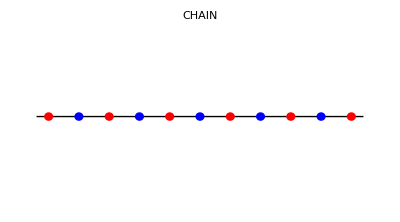

```mathematica
Chain=Graphics[{
Line[{{-.4,0},{10.4,0}}],
{Red,Disk[{0,0},.15]},
{Blue,Disk[{1,0},.15]},
{Red,Disk[{2,0},.15]},
{Blue,Disk[{3,0},.15]},
{Red,Disk[{4,0},.15]},
{Blue,Disk[{5,0},.15]},
{Red,Disk[{6,0},.15]},
{Blue,Disk[{7,0},.15]},
{Red,Disk[{8,0},.15]},
{Blue,Disk[{9,0},.15]},
{Red,Disk[{10,0},.15]},
{White,Point[{5,3}]},
{White,Point[{5,-3}]}}, PlotLabel->"CHAIN"]
```

```mathematica
AllFigures={Cube2, Cube3, Cube4, RectangularLattice, HexagonalLattice,SymmetricTree,Chain};
Manipulate[AllFigures⟦k⟧,{k,{1,2,3,4,5,6,7}}]
```

The following commands activate dynamic displays that appear on Slide 11:

```mathematica
Manipulate[Plot[PDF[BetaDistribution[α,β],x],{x,0,1}, PlotRange->{0,5},PlotLabel->"Assorted Beta Distributions"],{α,.5, 10},{β, .5, 10}]
```

```mathematica
Manipulate[Plot[{PDF[NormalDistribution[.5,0.0802],x],PDF[NormalDistribution[.5,0.2000],x],PDF[BetaDistribution[α,α],x]},{x,0,1},PlotRange->{0,5.2},PlotLabel->"Two Gaussians & Assorted Centered Beta Distributions"],{α,0.1, 20}]
```

```mathematica
Manipulate[Plot[2/(π B)√((B-x)/x),{x,0,20},PlotRange->{0,.5}, PlotStyle->{Thick, Red},PlotLabel->"Marchenko-Pastur Distributions"],{B,5,20}]
```